### Full Generality

```mathematica
γ = 2 - Sqrt[2];
d = γ/2;
w = Sqrt[2]/4;
α = ({{w}, {w}, {d}});
c0=({{0}, {γ}, {1}});
c1=({{c11}, {c12}, {c13}});
β1=({{β11}, {β12}, {β13}});
β2=({{β21}, {β22}, {β23}});
A0=({{0, 0, 0}, {d, d, 0}, {w, w, d}}); (* A0=({{A011, A012, A013}, {A021, A022, A023}, {A031, A032, A033}}); *)
B0=({{0, 0, 0}, {B021, 0, 0}, {B031, B032, 0}}); (* Subscript[B, 0]=({{B011, B012, B013}, {B021, B022, B023}, {B031, B032, B033}}); *)
H0=({{H01}, {H02}, {H03}});
VU=({{U}, {U}, {U}});
e = ({{1}, {1}, {1}});
```

```mathematica
K1=IdentityMatrix[3] - μ h A0 ;
MatrixForm[K1 ]
```

(1 | 0 | 0
-1/2 (2-√2) h μ | 1-1/2 (2-√2) h μ | 0
-(h μ)/(2 √2) | -(h μ)/(2 √2) | 1-1/2 (2-√2) h μ)

```mathematica
K2 = VU + B0 . e  σ (σ I10)/h;
MatrixForm[K2]
```

(U
U+(B021 I10 σ^2)/h
U+((B031+B032) I10 σ^2)/h)

```mathematica
H0= Inverse[K1].K2;
MatrixForm[H0]
```

((U (1-1/2 (2-√2) h μ)^2)/(1-2 h μ+√2 h μ+(3 h^2 μ^2)/2-√2 h^2 μ^2)
(U (h μ-(h μ)/(√2)-(3 h^2 μ^2)/2+√2 h^2 μ^2))/(1-2 h μ+√2 h μ+(3 h^2 μ^2)/2-√2 h^2 μ^2)+((1-h μ+(h μ)/(√2)) (U+(B021 I10 σ^2)/h))/(1-2 h μ+√2 h μ+(3 h^2 μ^2)/2-√2 h^2 μ^2)
(h U μ)/(2 √2 (1-2 h μ+√2 h μ+(3 h^2 μ^2)/2-√2 h^2 μ^2))+(h μ (U+(B021 I10 σ^2)/h))/(2 √2 (1-2 h μ+√2 h μ+(3 h^2 μ^2)/2-√2 h^2 μ^2))+((1-h μ+(h μ)/(√2)) (U+((B031+B032) I10 σ^2)/h))/(1-2 h μ+√2 h μ+(3 h^2 μ^2)/2-√2 h^2 μ^2))

```mathematica
U2= U+ μ h αᵀ.H0 + σ I1 Transpose[e].β1+ σ I10/h Transpose[e].β2;
U2 =U2[[1]][[1]];
U2
```

U+I1 (β11+β12+β13) σ+(I10 (β21+β22+β23) σ)/h+h μ ((U (1-1/2 (2-√2) h μ)^2)/(2 √2 (1-2 h μ+√2 h μ+(3 h^2 μ^2)/2-√2 h^2 μ^2))+((U (h μ-(h μ)/(√2)-(3 h^2 μ^2)/2+√2 h^2 μ^2))/(1-2 h μ+√2 h μ+(3 h^2 μ^2)/2-√2 h^2 μ^2)+((1-h μ+(h μ)/(√2)) (U+(B021 I10 σ^2)/h))/(1-2 h μ+√2 h μ+(3 h^2 μ^2)/2-√2 h^2 μ^2))/(2 √2)+1/2 (2-√2) ((h U μ)/(2 √2 (1-2 h μ+√2 h μ+(3 h^2 μ^2)/2-√2 h^2 μ^2))+(h μ (U+(B021 I10 σ^2)/h))/(2 √2 (1-2 h μ+√2 h μ+(3 h^2 μ^2)/2-√2 h^2 μ^2))+((1-h μ+(h μ)/(√2)) (U+((B031+B032) I10 σ^2)/h))/(1-2 h μ+√2 h μ+(3 h^2 μ^2)/2-√2 h^2 μ^2)))

```mathematica
I10=1/2 h(W+Z/(√3)); 
I1= W;
```

```mathematica
U2Full = U2
```

U+W (β11+β12+β13) σ+1/2 (W+Z/(√3)) (β21+β22+β23) σ+h μ ((U (1-1/2 (2-√2) h μ)^2)/(2 √2 (1-2 h μ+√2 h μ+(3 h^2 μ^2)/2-√2 h^2 μ^2))+((U (h μ-(h μ)/(√2)-(3 h^2 μ^2)/2+√2 h^2 μ^2))/(1-2 h μ+√2 h μ+(3 h^2 μ^2)/2-√2 h^2 μ^2)+((1-h μ+(h μ)/(√2)) (U+1/2 B021 (W+Z/(√3)) σ^2))/(1-2 h μ+√2 h μ+(3 h^2 μ^2)/2-√2 h^2 μ^2))/(2 √2)+1/2 (2-√2) ((h U μ)/(2 √2 (1-2 h μ+√2 h μ+(3 h^2 μ^2)/2-√2 h^2 μ^2))+(h μ (U+1/2 B021 (W+Z/(√3)) σ^2))/(2 √2 (1-2 h μ+√2 h μ+(3 h^2 μ^2)/2-√2 h^2 μ^2))+((1-h μ+(h μ)/(√2)) (U+1/2 (B031+B032) (W+Z/(√3)) σ^2))/(1-2 h μ+√2 h μ+(3 h^2 μ^2)/2-√2 h^2 μ^2)))

```mathematica
U2Plugged = U2Full /.  {W -> 0,Z->0}
G = Coefficient[U2Plugged,U]
```

U+h μ ((U (1-1/2 (2-√2) h μ)^2)/(2 √2 (1-2 h μ+√2 h μ+(3 h^2 μ^2)/2-√2 h^2 μ^2))+1/2 (2-√2) ((h U μ)/(√2 (1-2 h μ+√2 h μ+(3 h^2 μ^2)/2-√2 h^2 μ^2))+(U (1-h μ+(h μ)/(√2)))/(1-2 h μ+√2 h μ+(3 h^2 μ^2)/2-√2 h^2 μ^2))+((U (1-h μ+(h μ)/(√2)))/(1-2 h μ+√2 h μ+(3 h^2 μ^2)/2-√2 h^2 μ^2)+(U (h μ-(h μ)/(√2)-(3 h^2 μ^2)/2+√2 h^2 μ^2))/(1-2 h μ+√2 h μ+(3 h^2 μ^2)/2-√2 h^2 μ^2))/(2 √2))

1+(h μ)/(1-2 h μ+√2 h μ+(3 h^2 μ^2)/2-√2 h^2 μ^2)-(3 h^2 μ^2)/(2 (1-2 h μ+√2 h μ+(3 h^2 μ^2)/2-√2 h^2 μ^2))+(√2 h^2 μ^2)/(1-2 h μ+√2 h μ+(3 h^2 μ^2)/2-√2 h^2 μ^2)

```mathematica
stableeq = FullSimplify[G/.  {μ -> z/h}]
```

(2 (3+2 √2+z+√2 z))/(2+√2-z)^2

```mathematica
GG[z_]:=(2 (3+2 √2+z+√2 z))/(2+√2-z)^2
```

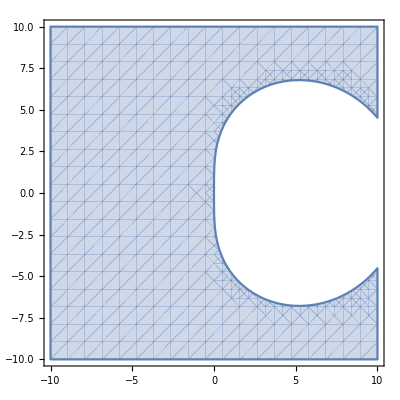

```mathematica
RegionPlot[Abs[GG[x+ⅈ y]]<1,{x,-10,10},{y,-10,10}]
```

```mathematica
cond1 = First[First[Transpose[α].e]] == 1;
cond2 = First[First[Transpose[β1].e]] == 1;
cond3 = First[First[Transpose[β2].e]] == 0;
cond4 = First[First[Transpose[α].B0.e]] == 1;
cond5 = First[First[Transpose[α].A0.e]] == 1/2;
cond6 = First[First[Transpose[α].(B0.e)^2]] == 3/2;
cond7 = First[First[Transpose[β1].c1]] == 1;
cond8 = First[First[Transpose[β2].c1]] == -1;
```

```mathematica
conds = {cond1,cond2,cond3,cond4,cond5,cond6,cond7,cond8}
vars = {β11,β12,β13,β21,β22,β23,B021,B031,B032,c11,c12,c13};
```

{True,β11+β12+β13==1,β21+β22+β23==0,B021/(2 √2)+1/2 (2-√2) B031+1/2 (2-√2) B032==1,True,B021^2/(2 √2)+1/2 (2-√2) (B031+B032)^2==3/2,c11 β11+c12 β12+c13 β13==1,c11 β21+c12 β22+c13 β23==-1}

```mathematica
FindInstance[conds ,vars,Reals]
```

{}